```mathematica
CBezX[a_,t_]:=3 a (1-t)^2 t+3 (1-a) (1-t) t^2+t^3
CBezY[b_,t_]:=3 b (1-t)^2 t+3 b (1-t) t^2
```

```mathematica
Pts[a_,b_]:={{0,0},{a,b},{1-a,b},{1,0}}
```

```mathematica
B1=4/3;
```

```mathematica
gθ[g_]:=If[g>0,ArcTan[π(1/g-1/2)]+π/2,0];
gx[t_,v_]:=Cos[t]Cos[gθ[v]]+t Sin[gθ[v]];
G[t_,v_]:=(gx[2π t,v]-gx[0,v])/(gx[π,v]-gx[0,v]);
Manipulate[
Magnify[ParametricPlot[
{G[t,g],Sin[2π t]},
{t,0,1},AspectRatio->1.1/2.1,PlotRange->{{-0.05,2.05},{-1.05,1.05}}],1.5],
{g,0,2}]
```

```mathematica
InvCBezXExpr=Solve[CBezX[a,t]==x,t];
InvCBezX1[a_,x_]:=Evaluate[InvCBezXExpr[[1,1,2]]];
InvCBezX2[a_,x_]:=Evaluate[InvCBezXExpr[[2,1,2]]];
InvCBezX3[a_,x_]:=Evaluate[InvCBezXExpr[[3,1,2]]];
InvCBezX[a_,x_]:=If[a<1/3,InvCBezX3,InvCBezX1][a,x]
```

```mathematica
Manipulate[
Magnify[Show[
ParametricPlot[{
{G[t,g],Sin[2π t]},
{CBezX[a,t],CBezY[B1,t]}
},{t,0,1},AspectRatio->1.1/2.1,PlotRange->{{-0.05,2.05},{-1.05,1.05}}],
Plot[
CBezY[B1,Re[InvCBezX[a,x]]],{x,0,1},PlotStyle->{Green}]
],1.5],
{a,0,1},{g,0,2}]
```

```mathematica
NMinimize[{
Sum[
(CBezY[B1,Re[InvCBezX[a,G[t/2,0]]]]-Sin[π t])^2,
{t,0,1,0.01}
],0.02<a<0.45},{a}]
```

{0.00965291,{a→0.0235523}}

```mathematica
ATop=Table[Pause[g];Print[g];
{g,NMinimize[{
Sum[
(CBezY[B1,Re[InvCBezX[a,G[t/2,g]]]]-Sin[π t])^2,
{t,0,1,0.01}
],0.02<a<0.45},{a}][[2,1,2]]},{g,0,2,0.05}]
```

0.

0.05

0.1

0.15

0.2

0.25

0.3

0.35

0.4

0.45

0.5

0.55

0.6

0.65

0.7

0.75

0.8

0.85

0.9

0.95

1.

1.05

1.1

1.15

1.2

1.25

1.3

1.35

1.4

1.45

1.5

1.55

1.6

1.65

1.7

1.75

1.8

1.85

1.9

1.95

2.

{{0.,0.0235523},{0.05,0.0343215},{0.1,0.0448302},{0.15,0.0551604},{0.2,0.0653602},{0.25,0.0754593},{0.3,0.0854771},{0.35,0.0954275},{0.4,0.10532},{0.45,0.115163},{0.5,0.124962},{0.55,0.134722},{0.6,0.144447},{0.65,0.154139},{0.7,0.163802},{0.75,0.173438},{0.8,0.183048},{0.85,0.192635},{0.9,0.2022},{0.95,0.211744},{1.,0.221268},{1.05,0.230773},{1.1,0.24026},{1.15,0.24973},{1.2,0.259184},{1.25,0.268623},{1.3,0.278046},{1.35,0.287454},{1.4,0.296849},{1.45,0.306229},{1.5,0.315597},{1.55,0.324951},{1.6,0.334293},{1.65,0.343623},{1.7,0.35294},{1.75,0.362246},{1.8,0.37154},{1.85,0.380823},{1.9,0.390095},{1.95,0.399356},{2.,0.408606}}

0.0282383+0.191462 g

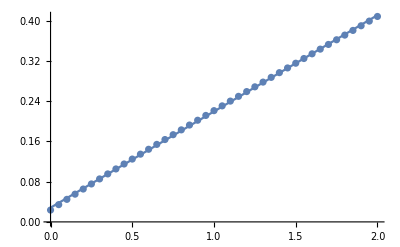

```mathematica
ag[x_]:=Evaluate[Fit[ATop,{1,x},x]];
ag[g]
Show[
ListPlot[ATop],
Plot[ag[g],{g,0,2}]
]
```

```mathematica
Manipulate[
Magnify[Show[
ParametricPlot[{
{G[t,g],Sin[2π t]},
{CBezX[ag[g],t],CBezY[B1,t]}
},{t,0,1},AspectRatio->1.1/2.1,PlotRange->{{-0.05,2.05},{-1.05,1.05}}]
],1.5],{g,0,2}]
```